```mathematica
Remove["Global`*"]
```

# Crosstalk

### ComplexMatrixDraw Code (copy to your Notebook, evaluate and use the ComplexMatrixDraw function)

Introduction: ComplexMatrixDraw daws a rectangular matrix of complex numbers cij as an array of cells with possibly
	- a frame and a central point
	- a 2D shape with an area proportional to |cij| or given by the optional function functionFor2DShapeArea(cij);
	- an arrow with angle arg(cij) and length  |cij| or given by the optional function  functionForArrowLength(cij);
	- a label.
	
Syntax: ComplexMatrixDraw[m,opts] with 
	m: a number, a vector (list of numbers) or a matrix (a list of list of numbers)
	opts: optional replacement rules of the type optionName->optionValue as described below:

Several options (with default behavior) are available:
	Options for the cell frame:
		- showFrame: True (default) or False. Draw a black square around each matrix cell
		- frameFaceFunction: function of the position ij returning directives for rendering the face of the square frame (default is {White, Opacity[0]}&, i.e. transparent)
		- showCentralPoint: True or False (default) wheter to draw a central point in the cell.
		- centralPointSize: parameter of the PointSize directive (Tiny,Small, Medium, or a relative size like 0.01 for example).
	Options for the 2D shape representing the complex number:
		- show2DShape: True (default) or False. Whether to draw the 2D shape or not.
		- whatShape: "circle" (default) or "square".
		- functionFor2DShapeAera: any  single argument function to be applied to cij to define the area of the 2D shape (default is Abs).
		- hide2DShapeSmallerThan: Value of functionFor2DShapeAera(cij) below which the 2D shape should not be drawn  (default is 0).
		- borderColor: Color of the 2D shape border (default is Black).
		- fill2DShape: whether to fill the 2Dshape (default is True);
		- fillingColor: Filling color function  f[ |cij| , arg(cij)] of the 2D shape. Default is Hue[#2/(2π)+0.5]&, i.e a cyclic color function of the phase arg(cij) that is cyan for φ=0 and red for φ=π . 
		- thicknessShape: thickness of the shape border (default is 0.01, i.e 1% of the cell).
	Options for the Arrow representing the complex Number
		- showArrow:  True (default) or False. wheter to draw the arrow or not.
		- functionForArrowLength: any  single argument function to be applied to cij to define the length of the arrow (default is Abs).
		- hideArrowSmallerThan: Value of functionForArrowLength(cij) below which the arrow should not be drawn  (default is 0).
		- thicknessArrow: thickness of the arrow border (default is 0.01, i.e 1% of the whole graph).
		- arrowColor: Color of the arow (default is Black).
		- arrowSize: Size of the arrow in fraction of the whole graph  (default is 0.05, i.e. 5%).
	Options for the label included in the cell
		- showLabel: True or False (default). Whether to write the number in the cell or not.
		- labelFunction: Function to apply to the number to form the label. Default is Identity
		- labelStyle: A directive for Style[], such as Small (default), Medium, Large, Red ...
		- labelShift: a list {Δx,Δy} (default is {0,0}) indicating how to shift the text in the cell.

```mathematica
Options[myPlotElement]=
{ 
showFrame->True,frameFaceFunction->({White,Opacity[0]}&),showCentralPoint->False,centralPointSize->Small,
show2DShape->True,whatShape->"circle",functionFor2DShapeAera->Abs,hide2DShapeSmallerThan->0,borderColor->Black,fill2DShape->True,fillingColor->(Hue[#2/(2π)+0.5]&),thicknessShape->.001,
showArrow->True,functionForArrowLength->Abs,hideArrowSmallerThan->0,thicknessArrow->.001,arrowSize->.05,arrowColor->Black,
showLabel->False, labelFunction->Identity, labelStyle->Small,labelShift->{0,0}
} ;
myPlotElement[c_,position_,OptionsPattern[]]:=
Block[
{center=(position-0.5{1,1}),
shapeAera=OptionValue[functionFor2DShapeAera][c],
arrowLength=OptionValue[functionForArrowLength][c],
φ=Arg[c],
frame={},shape={},arrow={},centralPoint={},number={}
},
If[OptionValue[showFrame],frame={{EdgeForm[Dashed],FaceForm[OptionValue[frameFaceFunction][position[[1]],position[[2]]]],Rectangle[center-0.5{1,-1},center+0.5{1,-1}]}}];
If[OptionValue[showCentralPoint],centralPoint={PointSize[OptionValue[centralPointSize]],Point[center]}];
If[OptionValue[show2DShape ]&& shapeAera>=OptionValue[hide2DShapeSmallerThan],
shape={EdgeForm[{Thickness[OptionValue[thicknessShape]],OptionValue[borderColor]}],If[OptionValue[fill2DShape],FaceForm[OptionValue[fillingColor][Abs[c],φ]],FaceForm[]]};
shape=Append[shape,
Switch[OptionValue[whatShape],
"square",Rectangle[center-Sqrt[shapeAera]/2,center+Sqrt[shapeAera]/2],
_,Disk[center,Sqrt[shapeAera]/2]]]];
If[OptionValue[showArrow] && arrowLength>=OptionValue[hideArrowSmallerThan],
arrow={OptionValue[arrowColor],Thickness[OptionValue[thicknessArrow]],Arrowheads[OptionValue[arrowSize]],Arrow[{center,center+0.5arrowLength{Cos[φ],Sin[φ]}}]}];
If[OptionValue[showLabel],number={Text[Style[OptionValue[labelFunction][c],OptionValue[labelStyle]],center+OptionValue[labelShift]]}];
Graphics[frame~Join~shape~Join~arrow~Join~centralPoint~Join~number]];
complexMatrixDraw[number_?NumberQ,opts___]:=complexMatrixDraw[{{number}},opts];
complexMatrixDraw[vector_?VectorQ,opts___]:=complexMatrixDraw[List/@vector,opts];
complexMatrixDraw[matrix_,opts___]:=Show[MapIndexed[myPlotElement[#1,(Reverse[#2]){1,-1},opts]&,matrix,{2}]];
```

### Crosstalk

```mathematica
path="L:\\local-expdata\\2 Qubit Experiments\\\\FO-C5\\3rd-Run\\2011_04_13\\";
```

```mathematica
detection=Import[path<>"detection_matrix.txt","Table"];
visibility=Import[path<>"visibility_matrix.txt","Table"];
crosstalk=Import[path<>"crosstalk_matrix.txt","Table"];
matrixSet={detection,visibility,crosstalk};
```

```mathematica
matrixSet={{{0.8201375,0.1518875,0.1768375,0.03115},{0.0698125,0.7275625,0.0164875,0.1720875},{0.1003125,0.0188,0.7341875,0.134725},{0.0097375,0.10175,0.0724875,0.6620375}},{{0.8222996559999999,0.15670169599999995,0.17906366390000003,0.0341233024},{0.07130034400000002,0.736898304,0.015526336100000008,0.16046669760000004},{0.09791034400000004,0.018658304000000004,0.7411463360999999,0.14123669759999996},{0.008489656000000007,0.08774169600000005,0.06426366390000002,0.6641733023999999}},{{0.9981627400842952,-0.005787041895118311,-0.0022207525903058262,-0.0025118892229731987},{-0.0007181511024154474,0.9849633965759865,-0.000050875236278256214,0.021177255365949},{0.004113336662040428,0.0005252345573518134,0.9903066155641249,-0.008081142767995125},{-0.001557925643920089,0.020298410761780045,0.011965012262459065,0.9894157766250193}}};
```

```mathematica
swapLines2And3={#[[1]],#[[3]],#[[2]],#[[4]]}&;
from0213To0123[ρ_]:=ρ//swapLines2And3//Transpose//swapLines2And3//Transpose
```

```mathematica
{detection,visibility,crosstalk}=matrixSet2=from0213To0123/@matrixSet;
```

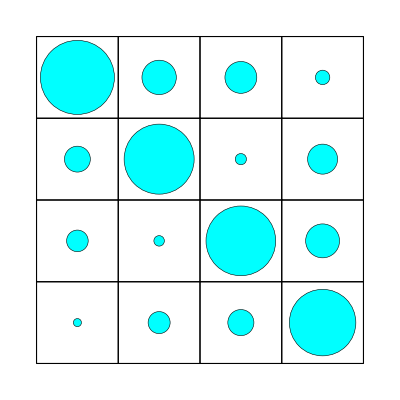
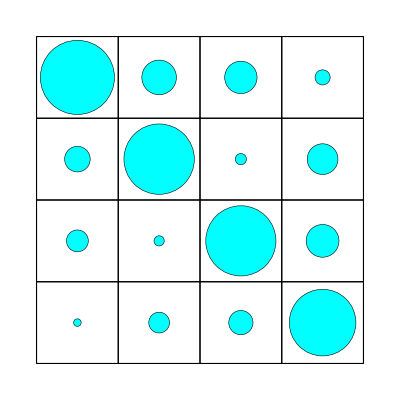
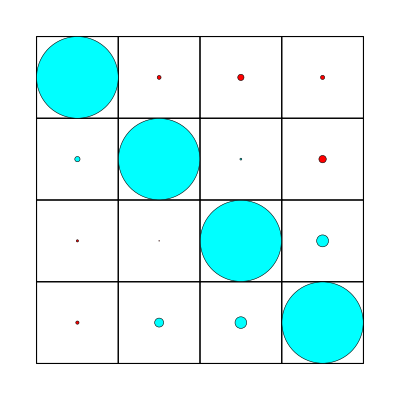

```mathematica
complexMatrixDraw[#,showArrow->False]&/@matrixSet2
```

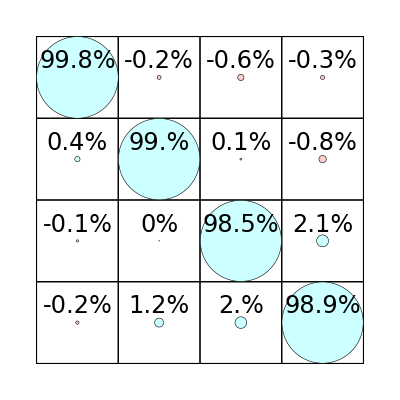

```mathematica
complexMatrixDraw[crosstalk,showArrow->False,showLabel->True,labelFunction->((ToString[Round[1000#]/10.]<>"%")&),labelStyle->{FontSize->24,FontFamily->"Arial"},labelShift->{0,0.2},fillingColor->(Hue[#2/(2π)+0.5,0.2,1]&)]
```

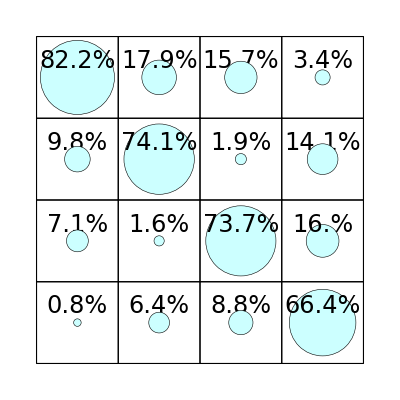

```mathematica
complexMatrixDraw[visibility,showArrow->False,showLabel->True,labelFunction->((ToString[Round[1000#]/10.]<>"%")&),labelStyle->{FontSize->24,FontFamily->"Arial"},labelShift->{0,0.2},fillingColor->(Hue[#2/(2π)+0.5,0.2,1]&)]
```

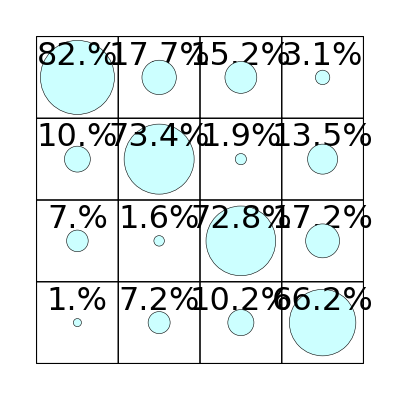

```mathematica
complexMatrixDraw[detection,showArrow->False,showLabel->True,labelFunction->((ToString[Round[1000#]/10.]<>"%")&),labelStyle->{FontSize->32,FontFamily->"Arial"},labelShift->{0,0.26},fillingColor->(Hue[#2/(2π)+0.5,0.2,1]&)]
```

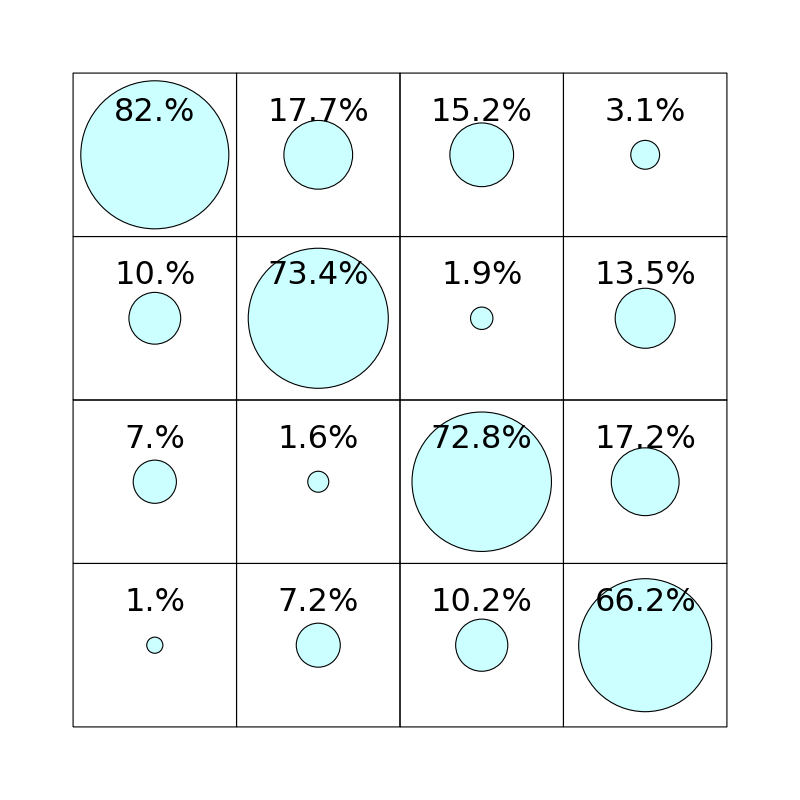

```mathematica
Show[%,ImageSize->800]
```

```mathematica
(r1={{0.93,0.09},{0.07,0.81}})//MatrixForm
(r2={{0.88,0.09},{0.12,0.81}})//MatrixForm
```

(0.93 | 0.09
0.07 | 0.81)

(0.88 | 0.09
0.12 | 0.81)

```mathematica
KroneckerProduct[r1,r2]//MatrixForm
```

(0.8184 | 0.0837 | 0.0792 | 0.0081
0.1116 | 0.7533 | 0.0108 | 0.0729
0.0616 | 0.0063 | 0.7128 | 0.0729
0.0084 | 0.0567 | 0.0972 | 0.6561)

-Graphics-